```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/data_v2/CPT

```mathematica
dataall=Import["Shi_CPT_m0=600_m0=600-flag_4-1600x17_VC=true.csv"];
```

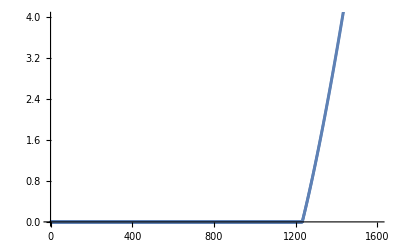

```mathematica
ListPlot[dataall[[1]]]
```

```mathematica
mub=Table[i,{i,800,960,(960.1-800)/1600}];
T=Table[i,{i,1,17,1}];
deltamub=(960.1-800)/1600;
```

```mathematica
mub[[501]]
mub[[1001]]
```

850.031

900.063

```mathematica
Clear[chi2data,chi4data,R42]
```

```mathematica
chi2data=Table[Table[(-dataall[[i]][[j+2]]+16dataall[[i]][[j+1]]-30dataall[[i]][[j]]+16dataall[[i]][[j-1]]-dataall[[i]][[j-2]])/(12 deltamub^2),{i,1,17}],{j,501,1001}];
chi4data=Table[Table[(-dataall[[i]][[j+3]]+12dataall[[i]][[j+2]]-39dataall[[i]][[j+1]]+56dataall[[i]][[j]]-39dataall[[i]][[j-1]]+12dataall[[i]][[j-2]]-dataall[[i]][[j-3]])/(6 deltamub^4),{i,1,17}],{j,501,1001}];
R42=chi4data/chi2data;
```

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

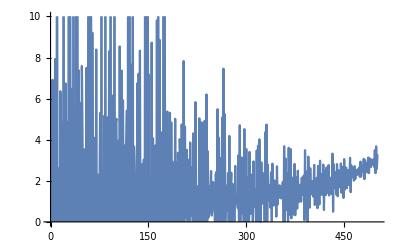

```mathematica
ListLinePlot[Transpose[R42][[13]]13^2,PlotRange->{All,{0,10}}]
```